## Import application packages

```mathematica
<<ProbabilisticBricks`
```

## Convergent horizontal loads - plastic zones interaction

### Problem initialization

Set the geometry and other parameters using setProblemProperties[nelx, nely, b, h, P, μ], where nelx is the number of bricks per course, nely the number of courses, b and h are the dimensions of the brick, P is the weight of a brick and μ the static friction coefficient

```mathematica
setProblemProperties[100,150,2,1,0.1,0.7];
```

Generate random contacts

```mathematica
generateContacts[];
```

### Boundary conditions - Loads

Initialize the vector of loads acting on top of the wall in the form of {... N_1,V_1,N_2,V_2,N_3,V_3...} where every group of six components represents the loads on a brick ordered from left to right

```mathematica
p=Table[{0,0,2,0,0,0},{nelx}];
p[[20;;22]]={0,0,40,40,0,0};
p[[78;;80]]={0,0,40,-80,0,0};
p=Flatten[p];
setBoundaryConditions[p];
```

### Solution

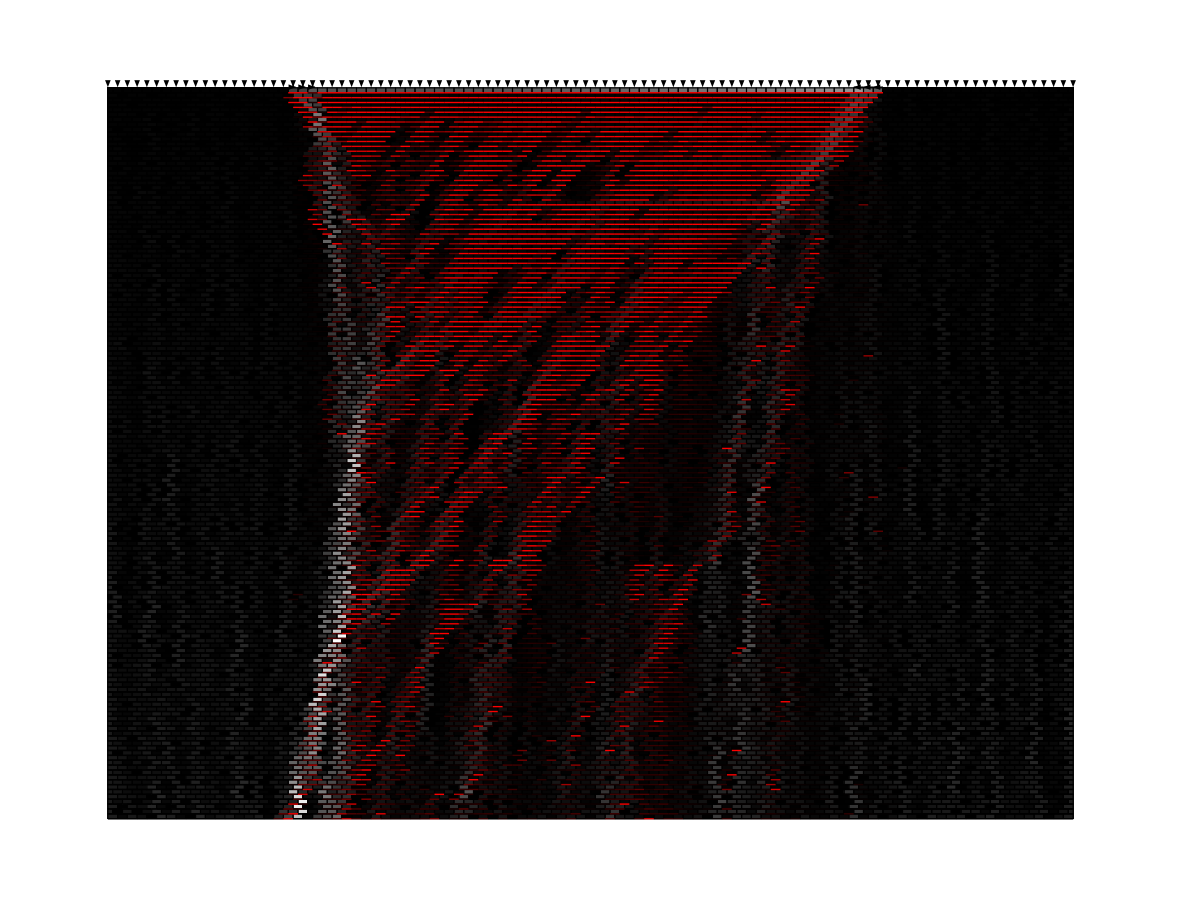

```mathematica
solveProblemAndDisplay["stress_state"]
(*displayWallWithFilter["contacts_state"]*)
```

### Compute frames

```mathematica
H1LoadingHistory[H1max_,t_]:=Piecewise[{{t,t≤H1max},{H1max,t>H1max}}];
H2LoadingHistory[H2max_,t_]:=Piecewise[{{t,t≤H2max}}];
```

```mathematica
H2max=80;H1max=40;
tmax=H2max;
frames={};
For[t=0,t≤tmax,t+=5,
p=Table[{0,0,2,0,0,0},{nelx}];
p[[20;;22]]={0,0,20,H1LoadingHistory[H1max,t],0,0};
p[[78;;80]]={0,0,20,-H2LoadingHistory[H2max,t],0,0};
p=Flatten[p];
setBoundaryConditions[p];
AppendTo[frames,solveProblemAndDisplay["stress_state"]];
];
```

## Convergent horizontal loads - plastic zones interaction

### Problem initialization

Set the geometry and other parameters using setProblemProperties[nelx, nely, b, h, P, μ], where nelx is the number of bricks per course, nely the number of courses, b and h are the dimensions of the brick, P is the weight of a brick and μ the static friction coefficient

```mathematica
setProblemProperties[100,100,2,1,0.1,0.7];
```

Generate random contacts

```mathematica
generateContacts[];
```

### Boundary conditions - Loads

Initialize the vector of loads acting on top of the wall in the form of {... N_1,V_1,N_2,V_2,N_3,V_3...} where every group of six components represents the loads on a brick ordered from left to right

```mathematica
p=Table[{0,0,0,0,0,0},{nelx}];
p[[35;;37]]={0,0,20,20,0,0};
p[[63;;65]]={0,0,20,-20,0,0};
p=Flatten[p];
setBoundaryConditions[p];
```

### Solution

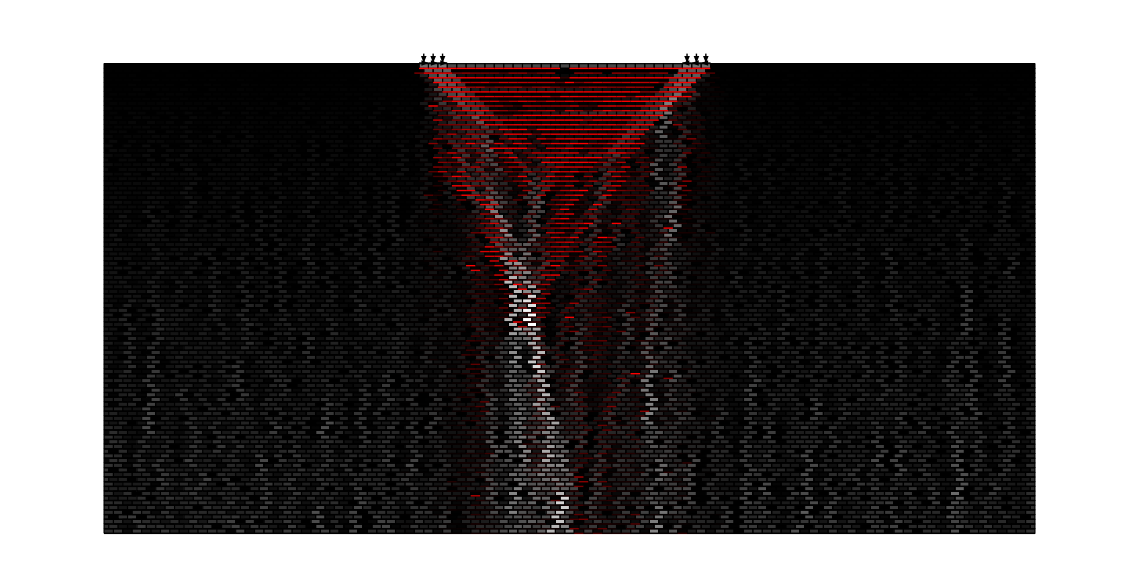

```mathematica
solveProblemAndDisplay["stress_state"]
(*displayWallWithFilter["contacts_state"]*)
```

### Compute frames

```mathematica
H1LoadingHistory[H1max_,t_]:=Piecewise[{{t,t≤H1max},{H1max,t>H1max}}];
H2LoadingHistory[H2max_,t_]:=Piecewise[{{t,t≤H2max}}];
loadingPath[h1_,h2_]:=Show[ParametricPlot[{H2LoadingHistory[H2max,t]/H1max,H1LoadingHistory[H1max,t]/H1max},{t,0,H2max},AxesLabel->{Style[Text[TraditionalForm["H_2/N"]],FontSize->14],Style[Text[TraditionalForm["H_1/N"]],FontSize->14]},Background->White],Graphics[{PointSize->Large,Point[{h2,h1}]}]]
H2max=40;H1max=20;
```

```mathematica
tmax=H2max;
frames={};
For[t=0,t≤tmax,t+=0.5,
p=Table[{0,0,0,0,0,0},{nelx}];
p[[35;;37]]={0,0,H1max,H1LoadingHistory[H1max,t],0,0};
p[[63;;65]]={0,0,H1max,-H2LoadingHistory[H2max,t],0,0};
p=Flatten[p];
setBoundaryConditions[p];
lpGraphics=loadingPath[H1LoadingHistory[H1max,t]/H1max,H2LoadingHistory[H2max,t]/H1max];
wallGraphics=solveProblemAndDisplay["stress_state"];
frame=Show[wallGraphics,Epilog->Inset[lpGraphics,Scaled[{0.935,0.055}],Scaled[{1,0}],Scaled[0.3]]];
AppendTo[frames,frame];
];
```

### Export frames as a video

```mathematica
Export["convergent_h_loads.avi",frames,"FrameRate"->3,ImageSize->{1280,Automatic}]
```

convergent_h_loads.avi

### Export every frame as a pdf

```mathematica
Do[
Export["~/convergent-h-loads/frame_"<>ToString[i]<>".pdf",frames[[i]],ImageSize->1280],
{i,Length[frames]}
];
```

### Save frames and contacts definitions in a separate file

Delete the old file before saving

```mathematica
Save["~/convergent-h-loads/data.m",frames]
Save["~/convergent-h-loads/data.m",contacts]
```